0.29

160

0.85

0.87113

0.85

39269.9

1.47655

3

{0.01,0.03,0.005}

102

{0,0,0,0,0}

{0,0,0,0,0}

{0,0,0,0,0}

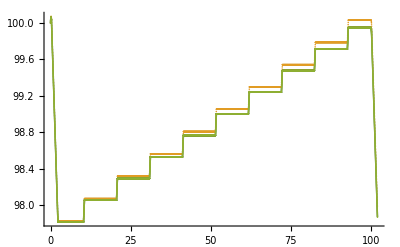

```mathematica
T=0.29
ph=160
rou0=0.85
Em[p_]:=0.0001*p^3-0.001082*p^2+5.474*p+1532/;0≤p<3000
rouh=N[rou0*E^Integrate[1/Em[x],{x,100,160}]]
c=0.85
v0=N[Pi*500*25]
s=N[Pi*0.47]
A[t_]:=s/;0<=Mod[t,T+10]<T
A[t_]:=0/;T≤Mod[t,T+10]<T+10
Qo[t_]:=N[100*Mod[t,100]]/;0≤Mod[t,100]<0.2
Qo[t_]:=20/;0.2≤Mod[t,100]<2.2
Qo[t_]:=N[-100(t-2.4)]/;2.2≤Mod[t,100]<2.4
Qo[t_]:=0/;2.4≤Mod[t,100]<100
size=3
delt={0.01,0.03,0.005}
len=102
t={0,0,0,0,0}
p={0,0,0,0,0}
td={0,0,0,0,0}
For[j=1,j<=size,j++,length=IntegerPart[len/delt[[j]]];total=(length+1)*delt[[j]];t[[j]]=Table[x,{x,0,total,delt[[j]]}];p[[j]]=Table[x,{x,0,total,delt[[j]]}];
For[i=2;p[[j]][[1]]=100,i≤length,i++,p[[j]][[i]]=N[p[[j]][[i-1]]+delt[[j]]*Em[p[[j]][[i-1]]]*(c*A[t[[j]][[i-1]]]*Sqrt[2*(ph-p[[j]][[i-1]])/rouh]-Qo[t[[j]][[i-1]]])/v0]];
td[[j]]=Table[{t[[j]][[i]],p[[j]][[i]]},{i,1,length,1}]]
ListPlot[td]
```

{0,0,0,0,0}

{0.1}

10

{0,0,0,0,0}

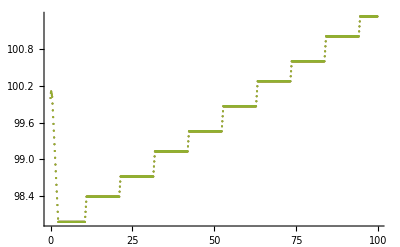

{0,0,0,0,0}

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.}

Set::partd: 部分指定 p⟦1,1⟧ 比对象深度更长.

Part::partd: 部分指定 0⟦1⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

Set::partd: 部分指定 p⟦1,i⟧ 比对象深度更长.

General::stop: 在本次计算中，Set::partd 的进一步输出将被抑制.

Part::pkspec1: 表达式 1.2 不能作为部分指定使用.

Part::pkspec1: 表达式 1.4 不能作为部分指定使用.

General::stop: 在本次计算中，Part::pkspec1 的进一步输出将被抑制.

```mathematica
{0,0,0,0,0}
```